```mathematica
NotebookEvaluate[NotebookDirectory[]<>"../setup.nb"]
```

```mathematica
abortOnMessageOn[]
```

Load pre-processed data

```mathematica
Get[NotebookDirectory[]<>"../../Data/WT/mesh-data.mx"]
```

## Cells colored by DV position

```mathematica
dvAngle[p_]:=-π+0.1+toCylinder[p][[2]]/$radius
```

```mathematica
dvStratifiedBodyCells=Join[
Table[
Select[bodyCells,ϕ<Abs[dvAngle[cellCentroidsTS[[1]][#]]]<ϕ+0.1π&],
{ϕ,0.2π,π-0.2π,0.1π}
],
{Select[bodyCells,π-0.1π<Abs[dvAngle[cellCentroidsTS[[1]][#]]]&]}
];
```

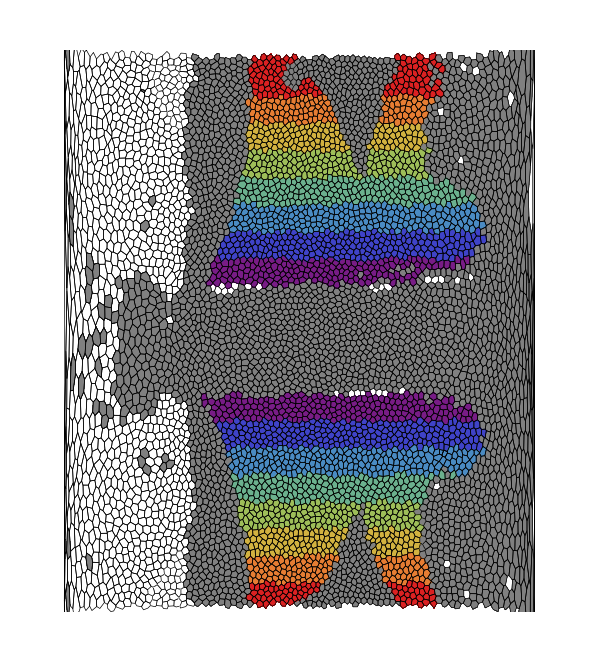

```mathematica
With[{t=1},Graphics[{
EdgeForm[{Black,AbsoluteThickness[0.5]}],FaceForm[White],
renderCellGroup2D[Complement[Keys[cellCentroidsTS[[t]]],invaginatingCells,Catenate[dvStratifiedBodyCells]],t],
FaceForm[Gray],
renderCellGroup2D[Intersection[Keys[cellCentroidsTS[[t]]],invaginatingCells],t],
Table[{
FaceForm[Blend[{ColorData["Rainbow"][(i-1)/(Length[dvStratifiedBodyCells]-1)],White},0]],
renderCellGroup2D[dvStratifiedBodyCells[[i]],t]
},
{i,Length[dvStratifiedBodyCells]}
]
},
PlotRange->{{5,510},{0,2π $radius}},
ImageSize->600,
Background->White
]]
```

Mark offspring from cell divisions in light gray

```mathematica
newCells[t_]:=Complement[Keys[cellVerticesTS[[t]]],Keys[cellVerticesTS[[t-1]]]]
```

```mathematica
daughterCellsTS=FoldList[Join[#1,#2]&,{},Table[Select[newCells[t],cellArea[#,t]>15.&],{t,2,198}]];
```

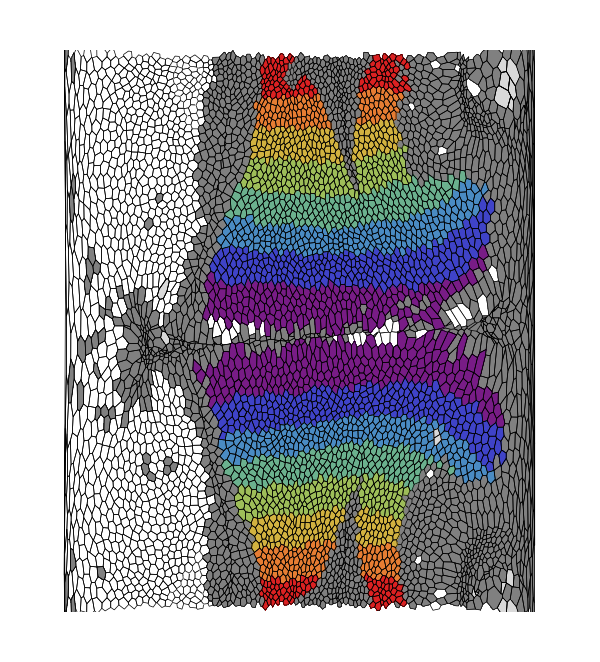

```mathematica
With[{t=100},Graphics[{
EdgeForm[{Black,AbsoluteThickness[0.5]}],FaceForm[White],
renderCellGroup2D[Complement[Keys[cellCentroidsTS[[t]]],invaginatingCells,Catenate[dvStratifiedBodyCells]],t],
EdgeForm[{Black,AbsoluteThickness[0.5]}],FaceForm[Gray],
renderCellGroup2D[Intersection[Keys[cellCentroidsTS[[t]]],invaginatingCells],t],
Table[{
FaceForm[Blend[{ColorData["Rainbow"][(i-1)/(Length[dvStratifiedBodyCells]-1)],White},0]],
renderCellGroup2D[dvStratifiedBodyCells[[i]],t]
},
{i,Length[dvStratifiedBodyCells]}
],
FaceForm[LightGray],
renderCellGroup2D[daughterCellsTS[[t]],t]
},
PlotRange->{{5,510},{0,2π $radius}},
ImageSize->600,
Background->White
]]
```

#### 3D rendering

```mathematica
With[{t=1},
Magnify[Graphics3D[{
EdgeForm[Black],AmbientLight[GrayLevel[0.7]],DirectionalLight[GrayLevel[0.5],ImageScaled[{-0.5,1,1}]],
GraphicsComplex[
vertexCoordsTS[[t]],{
Table[{
ColorData["Rainbow"][(i-1)/(Length[dvStratifiedBodyCells]-1)],
Polygon[cellVerticesTS[[t]][#]]&/@Intersection[Keys[cellCentroidsTS[[t]]],dvStratifiedBodyCells[[i]]]
},
{i,Length[dvStratifiedBodyCells]}
],
Gray,Polygon[cellVerticesTS[[t]][#]]&/@Intersection[invaginatingCells,Keys[cellCentroidsTS[[t]]]],
White,Polygon[cellVerticesTS[[t]][#]]&/@Complement[Keys[cellCentroidsTS[[t]]],Catenate[dvStratifiedBodyCells],invaginatingCells,daughterCellsTS[[t]]],
GrayLevel[0.7],Polygon[cellVerticesTS[[t]][#]]&/@Intersection[daughterCellsTS[[t]],Keys[cellCentroidsTS[[t]]]]
}
]
},
Boxed->False,Lighting->None,
ViewPoint->{0, -15,-100},ViewVertical->{0,-1,0},
Background->White,ImageSize->{500,250}
],
2
]]
```

-Graphics3D-

## Cell rearrangments

To identify cell rearrangements, we first identify all pairs of cells that are in contact (i.e. are neighbors) at at least one timepoint. For each pair of cells that are ever neighbors, we generate a time trace indicating whether they are neighbors (0 - no, 1 - yes) and whether both cells exists (-1 if at least one does not exist).

From these “contact timeseries”, we can then identify all edge collapse and creation events and all edges that are “permanent” (i.e. never collapse)

#### Generate cell pair contact timetraces (don’t run, load from file instead)

```mathematica
allNeighborAssoc=Union[Flatten[#]]&/@Association[Last@Reap[
KeyValueMap[Sow[#2,#1];&,#]&/@cellNeighborsTS,
_,Rule
]];//AbsoluteTiming
```

{1.67705,Null}

```mathematica
contactPairs=Union[Sort/@Catenate[KeyValueMap[Thread[{#1,#2}]&,allNeighborAssoc]]];//AbsoluteTiming
```

{0.033849,Null}

```mathematica
Length@contactPairs
```

37792

```mathematica
pairContactTS=Association[Thread[contactPairs->Transpose@Map[Function[{neighborAssoc},
Map[Function[{pair},
If[
KeyExistsQ[neighborAssoc,pair[[1]]]&&
KeyExistsQ[neighborAssoc,pair[[2]]],
If[MemberQ[neighborAssoc[pair[[1]]],pair[[2]]],1,0],
-1
]
],
contactPairs
]
],
cellNeighborsTS
]]];//AbsoluteTiming
```

{28.745,Null}

```mathematica
DumpSave[NotebookDirectory[]<>"../../Data/WT/pairContactTS.mx",pairContactTS];
```

```mathematica
Get[NotebookDirectory[]<>"../../Data/WT/pairContactTS.mx"]
```

#### Permanent edges

Helper function to drop the trailing segment of the time series where at least one of the cells is missing.

```mathematica
dropTrailingMissingCells[list_]:=Drop[list,1-First@FirstPosition[Reverse[list],Except[-1],{1},Heads->False]]
```

```mathematica
permanentPairs=Select[
Keys[Select[pairContactTS,Union[dropTrailingMissingCells[#]]=={1}&]],
Intersection[#,invaginatingCells]==={}&
];
```

#### Persistent collapses (Fig. 1E)

Find collapse events where the edge is no longer present at the last timepoint where both cells still exist. We call this “persistent” collapses. The complement to this are “unsuccessful” collapses, where the edge eventually reappears.

```mathematica
persistentCollapsesRaw=Select[
With[{l=dropTrailingMissingCells[#]},
If[l[[1]]==1&&l[[-1]]==0,First@FirstPosition[l,0,{-1}],-1]
]&/@pairContactTS,
Positive
];
```

Remove events that involve invaginating cells.

```mathematica
persistentCollapses=KeySelect[persistentCollapsesRaw,Not[MemberQ[invaginatingCells,#[[1]]]||MemberQ[invaginatingCells,#[[2]]]]&];
```

```mathematica
persistentCollapses//Length
```

2906

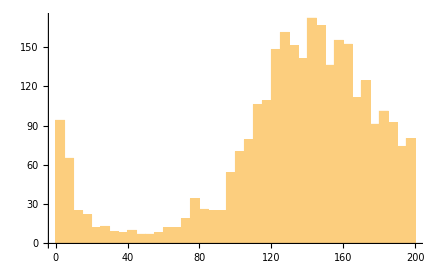

```mathematica
Histogram[persistentCollapses,{5}]
```

Rearrangement rates as a function of DV position

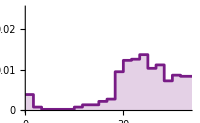
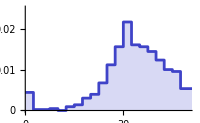
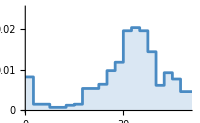
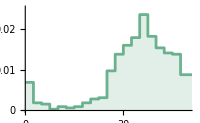
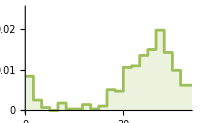
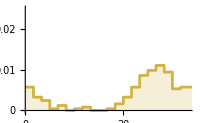
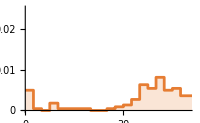
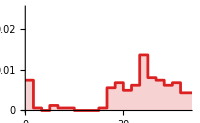

```mathematica
Table[
ListStepPlot[{
Transpose[{#[[1]]/4,1/Length[dvStratifiedBodyCells[[i]]]/10Append[#[[2]],#[[2,-1]]]}]&@HistogramList[KeySelect[persistentCollapses,Length[Intersection[#,dvStratifiedBodyCells[[i]]]]>0&],{0,200,10}]
},
PlotStyle->Directive[ColorData["Rainbow"][(i-1)/(Length[dvStratifiedBodyCells]-1)],AbsoluteThickness[2]],
Filling->Bottom,
PlotRange->{{0,All},{0,0.025}},PlotRangeClipping->False,
Ticks->{Range[0,50,10],{0,0.01,0.02}},
PlotTheme->"PDFExport",
ImageSize->200,ImagePadding->{{30,10},{25,10}}
],
{i,Length[dvStratifiedBodyCells]}
]
```

#### Timing of edge collapses

Timing indicated by color from cold (early) to warm (late)

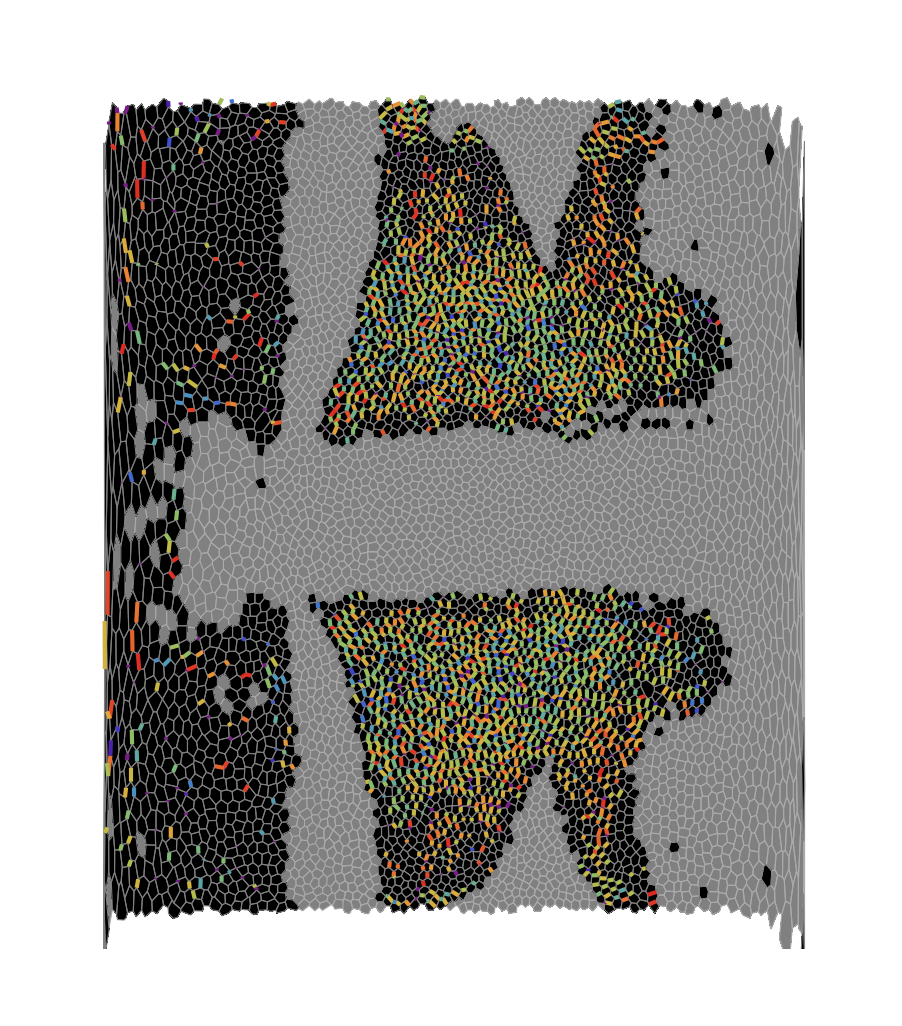

```mathematica
Graphics[{
EdgeForm[Lighter@Gray],FaceForm[Gray],
renderCell2D[#,1]&/@invaginatingCells,
EdgeForm[Gray],FaceForm[Black],
renderCell2D[#,1]&/@Complement[Keys[cellCentroidsTS[[1]]],Complement[invaginatingCells,isolatedInvaginatingCells]],
AbsoluteThickness[3],CapForm["Butt"],
Map[
Function[event,{ColorData["Rainbow"][(event[[2]]-50)/150],renderSharedEdge[event[[1]],1]}],
Reverse@SortBy[Normal[persistentCollapses],Last]
]
},
PlotRange->{{0,510},{-20,560}},
ImageSize->800
]
```

#### Orientation of collapsing edges (Fig. 1S2)

This requires the function ellipsoidBasis[] from pre-processing.nb

```mathematica
getEdgeOrientation[cellPair:{_Integer,_Integer},1]:=getEdgeOrientation[cellPair,1,"StaticFrame"];
getEdgeOrientation[cellPair:{_Integer,_Integer},t_Integer,"StaticFrame"]:=Module[{
v=sharedVertices[cellPair,t],
eVec,c,b
},
If[!MatchQ[v,{_Integer,_Integer}],
Return[Missing["SharedEdge",{cellPair,t}]]
];
{eVec,c}={#[[2]]-#[[1]],Mean[#]}&@vertexCoordsTS[[t,v]];
b=ellipsoidBasis[c];
ArcCos[Abs[b[[2]].Normalize[eVec-(eVec.b[[3]])b[[3]]]]]
]
```

Orientation relative to an advected frame (

```mathematica
getEdgeOrientation[cellPair:{_Integer,_Integer},1,"MovingFrame"]:=getEdgeOrientation[cellPair,1,"StaticFrame"];
getEdgeOrientation[cellPair_,t_,"MovingFrame"]:=Module[{
v=sharedVertices[cellPair,t],
eVec,c,b
},
If[!MatchQ[v,{_Integer,_Integer}],
Return[Missing["SharedEdge",{cellPair,t}]]
];
{eVec,c}={#[[2]]-#[[1]],Mean[#]}&@vertexCoordsTS[[t,v]];
b=transportLocalBasis[cellPair[[1]],1,t][[3]];
ArcCos[Abs[b[[2]].Normalize[eVec-(eVec.b[[3]])b[[3]]]]]
]
```

```mathematica
getEdgeOrientation[{1180,1181},1]
```

1.36657

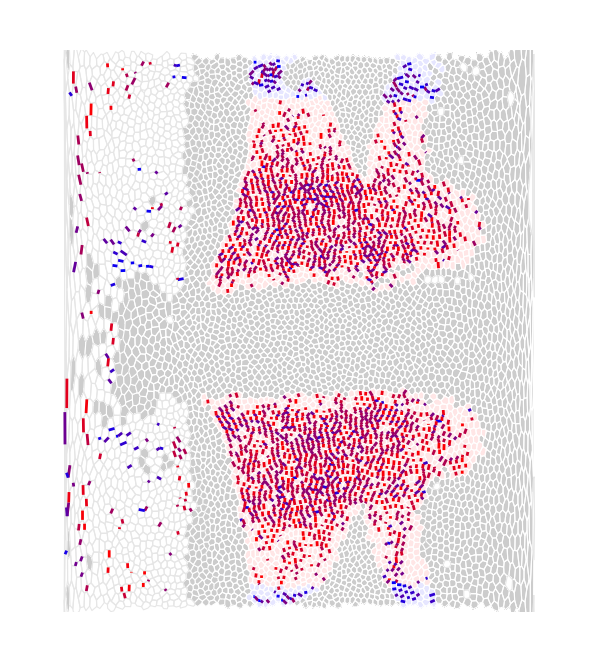

```mathematica
With[{t=1},Graphics[{
EdgeForm[White],FaceForm[GrayLevel[0.8]],
renderCellGroup2D[invaginatingCells,t],
EdgeForm[GrayLevel[0.9]],FaceForm[White],
renderCellGroup2D[Complement[Keys[cellCentroidsTS[[t]]],bodyCells,
Complement[invaginatingCells,isolatedInvaginatingCells]],t],
EdgeForm[GrayLevel[1]],
Blend[{White,Blue},0.1],renderCellGroup2D[bodyCellsDorsal,t],
Blend[{White,Red},0.1],renderCellGroup2D[Complement[bodyCells,bodyCellsDorsal],t],
AbsoluteThickness[2],CapForm["Butt"],
Map[
Function[arg,{Blend[{Red,Blue},getEdgeOrientation[arg[[1]],t]/(π/2)],renderSharedEdge[arg[[1]],t]}],
Reverse@SortBy[Normal[Select[persistentCollapses,50<#<200&]],Last]
]
},
PlotRange->{{5,510},{0,2π $radius}},
ImageSize->600,
Background->White
]]
```

```mathematica
orientationDataLateral=Catenate[Table[KeyValueMap[getEdgeOrientation[#1,t,"StaticFrame"]&,KeySelect[persistentCollapses,Length[Intersection[#,bodyCellsDorsal]]==0&]],{t,1,10}]];
```

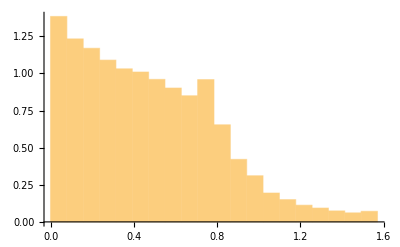

```mathematica
Histogram[orientationDataLateral,{0,π/2,π/40},"PDF"]
```

```mathematica
orientationDataDorsal=Catenate[Table[KeyValueMap[getEdgeOrientation[#1,t,"StaticFrame"]&,KeySelect[persistentCollapses,Length[Intersection[#,bodyCellsDorsal]]>0&]],{t,1,10}]];
```

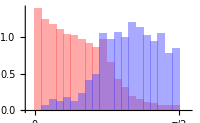

```mathematica
Histogram[{orientationDataLateral,orientationDataDorsal},{0,π/2,π/40},"PDF",
PerformanceGoal->"Speed",
ChartStyle->{
Directive[Opacity[0.5],EdgeForm[None],Lighter@Red],
Directive[Opacity[0.5],EdgeForm[None],Lighter@Blue]
},
PlotTheme->"PDFExport",
AxesOrigin->{-0.1,0},
PlotRange->{{-0.1,π/2+0.1},Automatic},
Ticks->{{0,π/4,π/2},{}},
ImageSize->200
]
```

Late collapses (after 42 min)

```mathematica
getEdgeOrientation[{15097,15132},100]
```

getEdgeOrientation[{15097,15132},100]

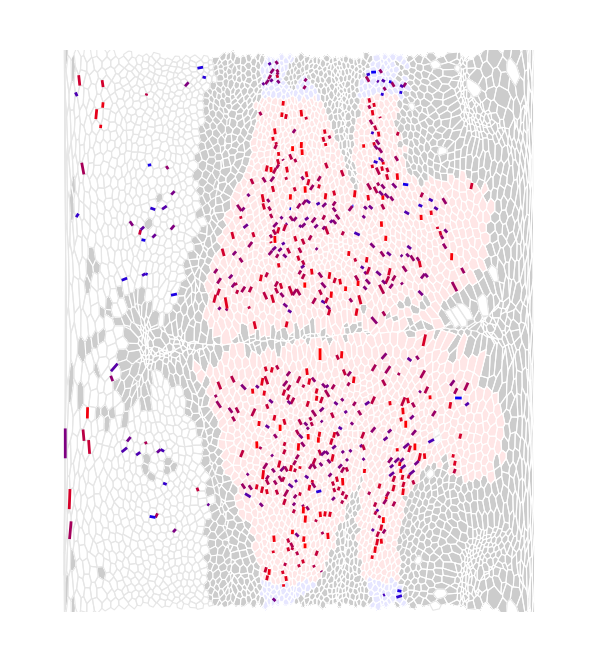

```mathematica
With[{t=100},Graphics[{
EdgeForm[White],FaceForm[GrayLevel[0.8]],
renderCellGroup2D[invaginatingCells,t],
EdgeForm[GrayLevel[0.9]],FaceForm[White],
renderCellGroup2D[Complement[Keys[cellCentroidsTS[[t]]],bodyCells,
Complement[invaginatingCells,isolatedInvaginatingCells]],t],
EdgeForm[GrayLevel[1]],
Blend[{White,Blue},0.1],renderCellGroup2D[bodyCellsDorsal,t],
Blend[{White,Red},0.1],renderCellGroup2D[Complement[bodyCells,bodyCellsDorsal],t],
AbsoluteThickness[2],CapForm["Butt"],
Map[
With[{angle=getEdgeOrientation[#[[1]],t,"StaticFrame"]},If[!MissingQ[angle],{Blend[{Red,Blue},angle/(π/2)],renderSharedEdge[#[[1]],t]}]]&,
Reverse@SortBy[Normal[Select[persistentCollapses,#>=4 42&]],Last]
]
},
PlotRange->{{5,510},{0,2π $radius}},
ImageSize->600,
Background->White
]]
```

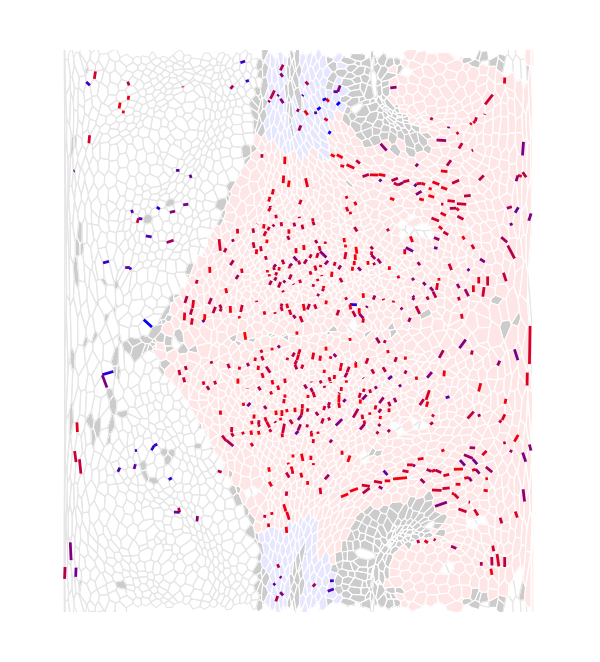

```mathematica
With[{t=150},Graphics[{
EdgeForm[White],FaceForm[GrayLevel[0.8]],
renderCellGroup2D[invaginatingCells,t],
EdgeForm[GrayLevel[0.9]],FaceForm[White],
renderCellGroup2D[Complement[Keys[cellCentroidsTS[[t]]],bodyCells,
Complement[invaginatingCells,isolatedInvaginatingCells]],t],
EdgeForm[GrayLevel[1]],
Blend[{White,Blue},0.1],renderCellGroup2D[bodyCellsDorsal,t],
Blend[{White,Red},0.1],renderCellGroup2D[Complement[bodyCells,bodyCellsDorsal],t],
AbsoluteThickness[2],CapForm["Butt"],
Map[
With[{angle=getEdgeOrientation[#[[1]],t,"MovingFrame"]},If[!MissingQ[angle],{Blend[{Red,Blue},angle/(π/2)],renderSharedEdge[#[[1]],t]}]]&,
Reverse@SortBy[Normal[Select[persistentCollapses,#>=170&]],Last]
]
},
PlotRange->{{5,510},{0,2π $radius}},
ImageSize->600,
Background->White
]]
```

Analyze the orientation of edges that collapse late (after 42 min) at various earlier timepoints.

```mathematica
lateCollapsesBody=KeySelect[Select[persistentCollapses,#>=4 42&],Length[Intersection[#,bodyCellsDorsal]]==0&];
```

```mathematica
Length[lateCollapsesBody]
```

568

```mathematica
orientationData100=Catenate[Table[KeyValueMap[getEdgeOrientation[#1,t,"MovingFrame"]&,lateCollapsesBody],
{t,100,105,1}
]];//AbsoluteTiming
```

{46.5715,Null}

```mathematica
orientationData150=Catenate[Table[KeyValueMap[getEdgeOrientation[#1,t,"MovingFrame"]&,lateCollapsesBody],
{t,150,155,1}
]];//AbsoluteTiming
```

{40.7898,Null}

```mathematica
orientationData1=Catenate[Table[KeyValueMap[getEdgeOrientation[#1,t,"StaticFrame"]&,lateCollapsesBody],{t,1,20}]];
```

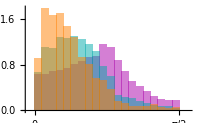

```mathematica
Histogram[{orientationData1,orientationData100,orientationData150},{0,π/2,π/40},"PDF",
PerformanceGoal->"Speed",
ChartStyle->{
Directive[Opacity[0.5],EdgeForm[None],Darker@Magenta],
Directive[Opacity[0.5],EdgeForm[None],Darker@Cyan],
Directive[Opacity[0.5],EdgeForm[None],Orange]
},
PlotTheme->"PDFExport",
AxesOrigin->{-0.1,0},
PlotRange->{{-0.1,π/2+0.1},Automatic},
Ticks->{{0,π/4,π/2},{}},
ImageSize->200
]
```

#### Number of edge collapses for each cell (Fig. 1S1D)

```mathematica
collapseCounts=With[{cells=Flatten[Keys[persistentCollapses]]},{#,Count[cells,#]}&/@Union[cells]];
```

```mathematica
MinMax[collapseCounts[[All,2]]]
```

{1,6}

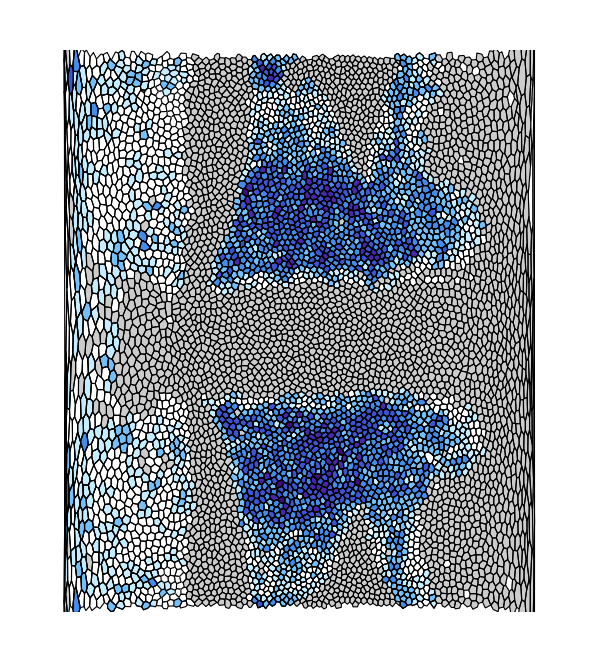

```mathematica
Graphics[{
EdgeForm[Black],FaceForm[GrayLevel[1]],
renderCellGroup2D[Complement[Keys[cellCentroidsTS[[1]]],invaginatingCells],1],
FaceForm[GrayLevel[0.8]],
renderCellGroup2D[invaginatingCells,1],
renderCellGroup2D[
Association[Map[
#[[1]]->FaceForm[ColorData["DeepSeaColors"][1-(#[[2]]-1)/6]]&,
collapseCounts
]],
1
]
},
PlotRange->{{5,510},{0,2π $radius}},
ImageSize->600,
Background->White
]
```

### T1s vs rosettes (Fig. 1E,E’)

#### Find all rosettes

Method to find rosettes: Connect all adjacent pairs of short edges (< 1 µm) by building a graph of the short edges and extracting the connected components with length > 3 and those including degenerate (four-fold) vertices.

```mathematica
rosetteLengthThreshold=1.;
rosetteCellsRawTS=Table[
With[{
degenerateVertices=First/@Position[vertexNeighborsTS[[t]],_?(Length[#]>3&),{1},Heads->False],
shortEdges=Select[edgeVerticesTS[[t]],Norm[vertexCoordsTS[[t,#[[1]]]]-vertexCoordsTS[[t,#[[2]]]]]<rosetteLengthThreshold&]
},
Union[Flatten[vertexCellsTS[[t,#]]]]&/@Select[ConnectedComponents[Graph[UndirectedEdge@@#&/@shortEdges]],Length[#]>2||Intersection[#,degenerateVertices]=!={}&]
],
{t,1,Length[cellCentroidsTS]}
];//AbsoluteTiming
```

{14.978,Null}

Remove all rosettes that involve cells other than body cells. This gets rid of rosettes that appear due to invaginations.

```mathematica
rosetteCellsTS=Select[
#,
Length[Intersection[#,bodyCells]]==Length[#]&
]&/@rosetteCellsRawTS;
```

Remove rosettes that have enclosed cells. These can be identified by checking whether there are multiple Hamiltoinan cycles (those visiting each vertex once) within a rosette candidate.

```mathematica
rosetteEnclosedCellQ[rosetteCells_,t_]:=With[{graph=makeGraph[rosetteCells,cellNeighborsTS[[t]]]},
Length[FindHamiltonianCycle[graph,All]]!=1
]
```

```mathematica
rosetteCellsTS=Table[Select[
rosetteCellsTS[[t]],
!rosetteEnclosedCellQ[#,t]&
],
{t,198}
];
```

```mathematica
Length[Catenate[rosetteCellsTS]]
```

2440

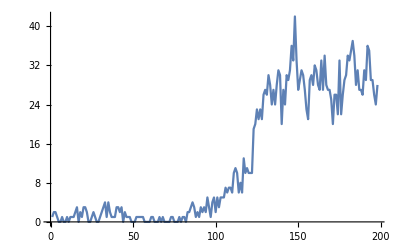

```mathematica
ListLinePlot[Length/@rosetteCellsTS]
```

#### Track rosettes across multiple frames

Identify rosettes at different timepoints as identical if at least 5 cells are identical between them

```mathematica
gatheredRosettes=Gather[Flatten[Table[{t,#}&/@rosetteCellsTS[[t]],{t,198}],1],Length[Intersection[#1[[2]],#2[[2]]]]>=5&];
```

```mathematica
rosettes7=Select[gatheredRosettes,Max[Length/@#[[All,2]]]==7&];
```

```mathematica
rosettes6=Select[gatheredRosettes,Max[Length/@#[[All,2]]]==6&];
```

```mathematica
rosettes5=Select[gatheredRosettes,Max[Length/@#[[All,2]]]==5&];
```

```mathematica
Length/@{rosettes5,rosettes6,rosettes7}
```

{498,40,4}

```mathematica
Length[persistentCollapses]-Length[rosetteCollapses]
```

2231

T1 and rosette counts (Fig. 1E’)

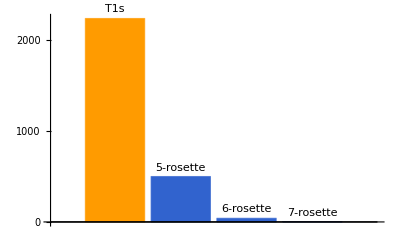

```mathematica
BarChart[{
Labeled[2231,"T1s",Above],
Labeled[498,"5-rosette",Above],
Labeled[40,"6-rosette",Above],
Labeled[4,"7-rosette",Above]
},
Ticks->{None,{0,1000,2000}},PerformanceGoal->"Speed",
ChartStyle->ColorData[112,"ColorList"][[{3,2,2,2}]]
]
```

Find outer edges via Hamilton cycle.

```mathematica
rosetteOuterEdges[rosetteCells_,t_]:=Module[{graph,cycles},
graph=makeGraph[rosetteCells,cellNeighborsTS[[t]]];
cycles=FindHamiltonianCycle[graph,All];
(* There should only be one Hamiltoinan cycle. Degenerate rosettes are caused by enclosed cells *)
If[Length[cycles]!=1,
Return[Missing["RosetteEnclosedCell",{rosetteCells,t}]]
];
{#[[1]],#[[2]]}&/@cycles[[1]]
]
```

Extract timepoints where the largest rosette in each “rosette sequence” exisits. Order the cells in the sequence of the outer edge cycle.

```mathematica
rosetteTimes=Association[Function[{rosetteSequence},With[{maxSize=Max[Length/@rosetteSequence[[All,2]]]},
rosetteOuterEdges[#[[1,2]],#[[1,1]]][[All,1]]->#[[All,1]]&@Select[rosetteSequence,Length[#[[2]]]==maxSize&]
]]/@gatheredRosettes];
```

```mathematica
checkRosette[cells_,t_]:=And@@MapThread[
MemberQ[cellNeighborsTS[[t]][#1],#2]&,
{cells,RotateLeft[cells]}
]
```

```mathematica
rosetteInnerEdges[cells_,t_]:=If[
!checkRosette[cells,t],
$Failed,
With[{
outerEdges=Sort/@Transpose[{cells,RotateLeft[cells]}],
allEdges=Sort/@findCellPairs[cells,t]
},
Complement[allEdges,outerEdges]
]
]
```

Render all rosettes that in the 30 timepoint window before they first reach their maximal size.

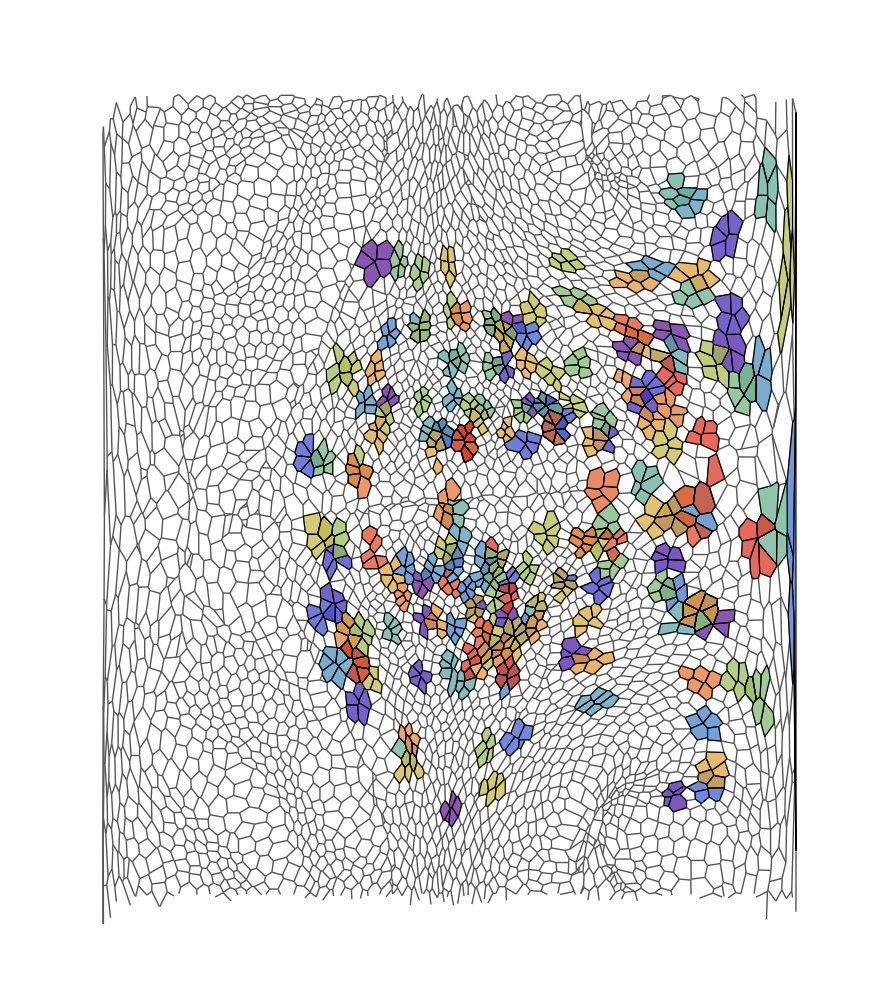

```mathematica
With[{t=140},
Graphics[{
FaceForm[LightGray],EdgeForm[Black],
(*Point[toCylinder/@Values[cellCentroidsTS[[t]]]],*)
{Darker@Gray,Line[toCylinder[vertexCoordsTS[[t,#]]]&/@edgeVerticesTS[[t]]]},
Opacity[0.75],
KeyValueMap[
{FaceForm[ColorData["Rainbow"][(First[#2]-(t))/(30)]](*FaceForm[RandomColor[]]*),renderCell2D[#,t]&/@#1}&,
Select[rosetteTimes,t<First[#]<t+30&]
]
},
PlotRange->{{0,510},{-10,560}}
]
]
```

#### Rosette contributions to T1 events (Fig. 1E)

Identify edge collapses that lead to rosette formation (rather than T1 events)

```mathematica
rosetteCollapses=With[{rosetteTimes=Normal[rosetteTimes]},
First@Last@Reap[Scan[
Function[{cellPair},
If[Length[#]!=0,Sow[{cellPair,#[[All,1]]}]]&@Select[
rosetteTimes,
And[
MemberQ[#[[1]],cellPair[[1]]],
MemberQ[#[[1]],cellPair[[2]]],
(* Check whether collapse takes place in an "outer edge" of the rosette *)
!MemberQ[Sort/@rosetteOuterEdges[#[[1]],#[[2,1]]],Sort@cellPair]
]&]
],
Keys[persistentCollapses]
]
]];//AbsoluteTiming
```

{5.10064,Null}

```mathematica
rosetteCollapses//Length
```

675

Some edges participate in multiple rosettes (see “gathered rosettes” above).

```mathematica
KeySort[Counts[Length[#[[2]]]&/@rosetteCollapses]]
```

<|1→578,2→73,3→22,4→1,5→1|>

```mathematica
persistentCollapses//Length
```

2906

```mathematica
rosetteCollapses//Length
```

675

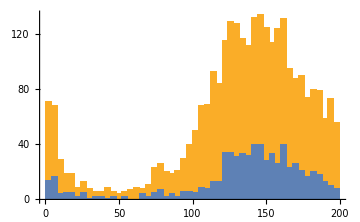

```mathematica
withOuterTicks[Histogram[{
Values[persistentCollapses],
persistentCollapses/@rosetteCollapses[[All,1]]
},{4},
PerformanceGoal->"Speed",
ChartStyle->Directive[EdgeForm[None],Opacity[1]]
],6]
```

```mathematica
Length[Select[rosetteCollapses[[All,1]],persistentCollapses[#]>50&]]
```

615

```mathematica
Length[Select[persistentCollapses,#>50&]]
```

2640

Excluding the first 50 timepoints, we have about 2000 collapses that should belong to T1s.